## Calculating Phase/ Fidelity for the Phenomological Approach

```mathematica
Pathh=NotebookDirectory[]
```

/home/bill/Documents/Third Paper Files/Paper Plots/Fig 4/

```mathematica
(*Some useful general functions*)
```

```mathematica
Clear[Savefun,CallFun,PlotFid,PlotPhase,PlotFidComp,PlotPhaseComp]
```

```mathematica
SaveFun[filename_,Data_]:=Export[StringJoin[{Pathh,"Data/",filename,".dat"}],Data]

Callfun[filename_]:=Import[StringJoin[{Pathh,"Data/",filename,".dat"}],"TSV"]

filenamefun[Name_,gsq_,α_,nmax_]:=StringJoin[{Name,"ArrayDelta",ToString[α],"gsq",ToString[gsq],"nmax",ToString[nmax]}]
```

## Plotting only

{}

{{10,50},Automatic}

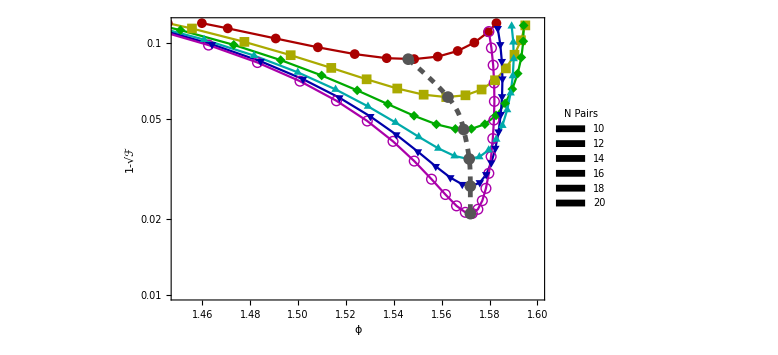

```mathematica
nlist={20,24,28,32,36,40};

σω=1.;
τ0=0.;
α=1.;
phaseplot={}
fidplot={};
infidplot={};
phasedifplot={};
maxfidtable={};
polarplot={};
fidphase={};

Infidcalc[data_]:=N[Table[{data[[i]][[1]],Abs[1-data[[i]][[2]]]},{i,1,Length[data]}]]
PhaseDifCalc[data_]:=N[Table[{data[[i]][[1]],π/2-data[[i]][[2]]},{i,1,Length[data]}]]
Polarize[data_]:=
N[Table[Abs[data[[i]]]*{Cos[Arg[data[[i]]]],Sin[Arg[data[[i]]]]},{i,1,Length[data]}]]
Fidphase[datafid_,dataphase_]:=
Block[{fiddat,phasedat},
fiddat=Sort[datafid];phasedat=Sort[dataphase];
N[Table[{phasedat[[i]][[2]],1-fiddat[[i]][[2]]},{i,1,Length[fiddat]}]]]

Do[{n=nlist[[p]],

filename=StringJoin["Gaussian_Markov_Freq_PhaseFid_n_",ToString[n],"_01"],

saveddata=ToExpression[Callfun[filename]],
rawtable=Sort[saveddata[[3]]],
phasetable=Sort[saveddata[[4]]],
fidtable=Sort[saveddata[[5]]],
AppendTo[maxfidtable,Abs[rawtable]],

AppendTo[fidplot,Abs[fidtable]],
AppendTo[phaseplot,Abs[phasetable]],
AppendTo[infidplot,Infidcalc[fidtable]],
AppendTo[phasedifplot,PhaseDifCalc[phasetable]],
AppendTo[polarplot,Polarize[rawtable]],
AppendTo[fidphase,Fidphase[fidtable,phasetable]]



},{p,1,Length[nlist]}]



legend=SwatchLegend[nlist/2,LegendMarkers->Graphics[{EdgeForm[Black],Rectangle[]}],LegendMargins->5,LabelStyle->{FontSize->20,GrayLevel[.4],FontWeight->Bold},LegendLabel->"N Pairs"];

pltrge={{10,50},Automatic}

maxphasefidlist={{1.546034325932871,0.08629909092894164},{1.5626201935458315,0.060992516978209975},{1.5691821621047544,0.045336763397954026},{1.571516567190368,0.03461144568384428},{1.5719722999305898,0.026990034463366352},{1.5719930341900596,0.020974419065265846}};

Plota=
Show[
ListLogPlot[fidphase,Axes->False,Frame->{True,True,True,True},FrameTicks->{All,All,None,None},PlotLegends->legend,FrameTicksStyle->Directive[FontSize->15,FontWeight->"Bold"],ImageSize->Large,FrameLabel->{{Style["1-√ℱ",FontSize->20,FontWeight->"Bold"]," "},{Style["ϕ",FontSize->20,FontWeight->"Bold"],Style["",FontSize->20,FontWeight->"Bold"]}},GridLines->{{π/2},{}},GridLinesStyle->Directive[Gray,Thick,Dashed],PlotRange->{{1.45,1.6},{0.01,.12}},Joined->True,PlotStyle->Table[Darker[Hue[i/(Length[nlist])]],{i,0,Length[nlist]-1}],PlotMarkers->{Automatic,10}],
ListLogPlot[maxphasefidlist,PlotStyle->{Darker[Gray],Dashed,Thickness[.006]},Joined->True,InterpolationOrder->3],
ListLogPlot[maxphasefidlist,PlotStyle->{Darker[Gray],Dashed,Thickness[.005]},Joined->False,PlotMarkers->{Automatic,12}]

]

Export[StringJoin[{Pathh,"NoInt_Phase_vs_Fid.png"}],Plota]
Export[StringJoin[{Pathh,"NoInt_Phase_vs_Fid.pdf"}],Plota]
Export[StringJoin[{Pathh,"NoInt_Phase_vs_Fid.eps"}],Plota]
```